```mathematica
SetDirectory[NotebookDirectory[]];
Import["https://qtechtheory.org/QuESTlink.m"]
CreateDownloadedQuESTEnv[];	
Needs["CCompilerDriver`"];
```

```mathematica
(* functions for obtaining the fit parameters of analytic descent *)
getEnergyAt1ShiftedParam[shift_,ind_,prmsIN_]:=Module[{prms},
prms=prmsIN;
prms[[ind,2]]=prms[[ind,2]]+shift;
ApplyCircuit[circ/.prms,InitZeroState@ψ];
Return@CalcExpecPauliSum[ψ,hamil,ϕ]
];

getEnergyAt2ShiftedParams[shift1_,shift2_,ind1_,ind2_,prmsIN_]:=Module[{prms},
prms=prmsIN;
prms[[ind1,2]]=prms[[ind1,2]]+shift1;
prms[[ind2,2]]=prms[[ind2,2]]+shift2;
ApplyCircuit[circ/.prms,InitZeroState@ψ];
Return@CalcExpecPauliSum[ψ,hamil,ϕ]
]

getFitParamters[params_,nPrms_]:=Module[{a,b,c,d},
a={getEnergyAt1ShiftedParam[0,1,params]};
b=Table[(getEnergyAt1ShiftedParam[π/2,n,params]
-getEnergyAt1ShiftedParam[-π/2,n,params])
,{n,1,nPrms}];
c=Table[getEnergyAt1ShiftedParam[π,n,params],{n,1,nPrms}];

d=Flatten@Table[If[k<l,
(getEnergyAt2ShiftedParams[-π/2,-π/2,k,l,params]
-getEnergyAt2ShiftedParams[-π/2,π/2,k,l,params]
-getEnergyAt2ShiftedParams[π/2,-π/2,k,l,params]
+getEnergyAt2ShiftedParams[π/2,π/2,k,l,params]
),0]
,{k,1,nPrms},{l,1,nPrms}];
Return@Join[a,b,c,d];
]
```

```mathematica
(* Define problem Hamiltonian and the ansatz circuit *)
numQs=6;
J=0.05;
noise=False;
hamil=0.05 Subscript[X, 0] Subscript[X, 1]+0.05 Subscript[X, 1] Subscript[X, 2]+0.05 Subscript[X, 2] Subscript[X, 3]+0.05 Subscript[X, 3] Subscript[X, 4]+0.05 Subscript[X, 0] Subscript[X, 5]+0.05 Subscript[X, 4] Subscript[X, 5]+0.05 Subscript[Y, 0] Subscript[Y, 1]+0.05 Subscript[Y, 1] Subscript[Y, 2]+0.05 Subscript[Y, 2] Subscript[Y, 3]+0.05 Subscript[Y, 3] Subscript[Y, 4]+0.05 Subscript[Y, 0] Subscript[Y, 5]+0.05 Subscript[Y, 4] Subscript[Y, 5]-0.7098301012032957 Subscript[Z, 0]-0.05177915010485945 Subscript[Z, 1]+0.05 Subscript[Z, 0] Subscript[Z, 1]+0.9065658350752286 Subscript[Z, 2]+0.05 Subscript[Z, 1] Subscript[Z, 2]-0.9265872629174545 Subscript[Z, 3]+0.05 Subscript[Z, 2] Subscript[Z, 3]+0.09500423337423802 Subscript[Z, 4]+0.05 Subscript[Z, 3] Subscript[Z, 4]-0.4959779888875864 Subscript[Z, 5]+0.05 Subscript[Z, 0] Subscript[Z, 5]+0.05 Subscript[Z, 4] Subscript[Z, 5];

circ={Subscript[Rx, 0][Subscript[θ, 1]],Subscript[Rx, 1][Subscript[θ, 2]],Subscript[Rx, 2][Subscript[θ, 3]],Subscript[Rx, 3][Subscript[θ, 4]],Subscript[Rx, 4][Subscript[θ, 5]],Subscript[Rx, 5][Subscript[θ, 6]],R[Subscript[θ, 7],Subscript[Z, 0] Subscript[Z, 1]],R[Subscript[θ, 8],Subscript[Z, 1] Subscript[Z, 2]],R[Subscript[θ, 9],Subscript[Z, 2] Subscript[Z, 3]],R[Subscript[θ, 10],Subscript[Z, 3] Subscript[Z, 4]],R[Subscript[θ, 11],Subscript[Z, 4] Subscript[Z, 5]],R[Subscript[θ, 12],Subscript[Z, 0] Subscript[Z, 5]],Subscript[Ry, 0][Subscript[θ, 13]],Subscript[Ry, 1][Subscript[θ, 14]],Subscript[Ry, 2][Subscript[θ, 15]],Subscript[Ry, 3][Subscript[θ, 16]],Subscript[Ry, 4][Subscript[θ, 17]],Subscript[Ry, 5][Subscript[θ, 18]],Subscript[Rx, 0][Subscript[θ, 19]],Subscript[Rx, 1][Subscript[θ, 20]],Subscript[Rx, 2][Subscript[θ, 21]],Subscript[Rx, 3][Subscript[θ, 22]],Subscript[Rx, 4][Subscript[θ, 23]],Subscript[Rx, 5][Subscript[θ, 24]],R[Subscript[θ, 25],Subscript[Z, 0] Subscript[Z, 1]],R[Subscript[θ, 26],Subscript[Z, 1] Subscript[Z, 2]],R[Subscript[θ, 27],Subscript[Z, 2] Subscript[Z, 3]],R[Subscript[θ, 28],Subscript[Z, 3] Subscript[Z, 4]],R[Subscript[θ, 29],Subscript[Z, 4] Subscript[Z, 5]],R[Subscript[θ, 30],Subscript[Z, 0] Subscript[Z, 5]],Subscript[Ry, 0][Subscript[θ, 31]],Subscript[Ry, 1][Subscript[θ, 32]],Subscript[Ry, 2][Subscript[θ, 33]],Subscript[Ry, 3][Subscript[θ, 34]],Subscript[Ry, 4][Subscript[θ, 35]],Subscript[Ry, 5][Subscript[θ, 36]],Subscript[Rx, 0][Subscript[θ, 37]],Subscript[Rx, 1][Subscript[θ, 38]],Subscript[Rx, 2][Subscript[θ, 39]],Subscript[Rx, 3][Subscript[θ, 40]],Subscript[Rx, 4][Subscript[θ, 41]],Subscript[Rx, 5][Subscript[θ, 42]]};
nPrms=Length@circ;


ψ = CreateQureg[numQs];
ϕ = CreateQureg[numQs];
hψ= CreateQureg[numQs];
dψ0= CreateQuregs[numQs,nPrms];
```

```mathematica
(* Compile analytic descent C code *)
LibraryUnload[aDescLib];
SetDirectory[NotebookDirectory[]];
(* We already know the number of parameters at compile time *)
compileFlag=ToString@StringForm["MAXDIM=``",nPrms];
aDescLib=CreateLibrary[{"analytic-descent.c"},"aDescLib","Debug"->False,"Defines"->compileFlag];
computeGradientLOCAL=LibraryFunctionLoad[aDescLib,"compute_gradient",{{Real,1},Integer},{Real,1}];
computeGradient[dat_,ths_,nPrms_]:=With[
{temp=computeGradientLOCAL[Join[dat,ths],nPrms]},
Return[{temp[[1]],temp[[2;;]]}]
];
```

LibraryUnload::strfile: String or valid File object is expected at position 1 in LibraryUnload[aDescLib]. A valid File has the form File[string].

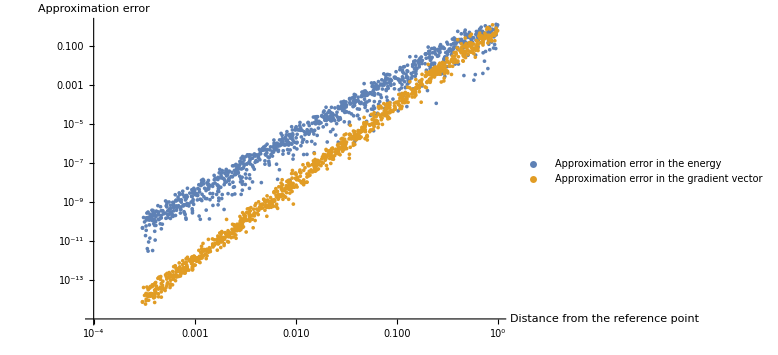

```mathematica
(* Fix a random reference point in parameter space*)
referenceParams=Table[Subscript[θ, k]->RandomReal[{-π,π}],{k,1,nPrms}];
(* deterime the fit parameters at the reference point *)
analyticDescentFit=getFitParamters[referenceParams,nPrms];

(* compute approximation errors at random points around the reference point *)
errors=Transpose@Table[
randomDisplacement=(10^RandomReal[{-3.5,0}])*RandomReal[{-1,1},nPrms];
{energyAnalytic,gradientAnalytic}=computeGradient[analyticDescentFit,randomDisplacement,nPrms];
params=referenceParams;
params[[;;,2]]=params[[;;,2]]+randomDisplacement;

CalcQuregDerivs[circ, InitZeroState[ψ], params, dψ0];
ApplyCircuit[circ/.params,InitZeroState@ψ];
energyExact= CalcExpecPauliSum[ψ, hamil, ϕ];
ApplyPauliSum[ψ, hamil, hψ];
gradientExact= 2CalcInnerProducts[hψ, dψ0] // Re;

similarity=1-(gradientExact.gradientAnalytic)/Norm[gradientExact]/Norm[gradientAnalytic];
dispNorm=Max@Abs@randomDisplacement;
{{dispNorm,Abs[energyAnalytic-energyExact]},{dispNorm,similarity}}
,{1000}];

ListPlot[errors,
PlotLegends->{"Approximation error in the energy","Approximation error in the gradient vector"},
AxesLabel->{"Distance from the reference point","Approximation error"}
,AxesOrigin->{10^(-4),10^(-15)},ImageSize->Large,ScalingFunctions->{"Log10","Log10"}
]
```

```mathematica
(* Determining slopes in the above graph *)
fit1=LinearModelFit[Log10@errors[[1]],x,x];
fit2=LinearModelFit[Log10@errors[[2]],x,x];
Print["Approximation error in the enrgy decreases in order: ",fit1[[1,2,2]]]
Print["Approximation error in the gradient vector decreases in order: ",fit2[[1,2,2]]]
```

Approximation error in the enrgy decreases in order: 2.91982

Approximation error in the gradient vector decreases in order: 3.98816